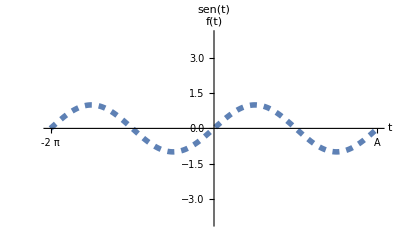

```mathematica
(* Comandos usan [], listas o estructuras de almacenamiento usan {}, metodos usan -> *)
(* Si pones xy wolfram piensa que es el nombre de una variable, si pones x y, como tiene espacio, wolfram piensa que es el producto x * y *)
(* Ctrl + 6: exponentes
Con tab mueves entre espacios de escritura, el actual espacio se pinta en azul. 
Alt + arriba o abajo con mouse: zoom a un plot (debe hacerse sobre el plot) *)
(* Tienes un metodo, por ejemplo PlotTheme, y quiero que el tema sea tanto Detailed como clasico, entonces cambias el input del metodo por una lista de parámetros dentro de {}
A cualquier constante de texto ("") se le puede hacer un StyleForm *)
Plot[Sin[x], {x, -2Pi, 2Pi}, PlotRange-> {-8/2, 8/2}, PlotStyle ->{Dashed, Thickness[0.01]}, AxesLabel->{StyleForm["t", Bold, 20], "f(t)" }, Ticks -> {{-2Pi, {2Pi, "A"}}, None }, PlotLabel-> "sen(t)"]
```

```mathematica
Plot3D[√(x^2+y^2), {x, -4, 4}, {y, -4, 4}, PlotLabel -> "Cono (coordenadas cartesianas)", PlotTheme->"Automatic"](* Cono con Plot3D, y este comando necesita funciones*)
ParametricPlot3D[{{r Cos[t], r Sin[t], r}}, {r,0, 2 }, {t, 0, 2Pi}, Mesh -> None, PlotStyle -> {Opacity[0.5]}, PlotLabel -> "Cono (coordenadas polares)", PlotTheme-> "Detailed"]
(* Si no tienes o quieres comandos, mejor parametrizas con coordenadas polares *)
(* Si definimos parametrización en coordenadas cartesianas, tendríamos x = u, y = v, donde z (dependiente) resultaría igual. Como no sirve, usamos parametrizaciones llamadas coordenadas polares, esféricas, etc.  *)
ParametricPlot3D[{{r Cos[t], r Sin[t], r^2}}, {r,0, 2 }, {t, 0, 2Pi}, Mesh -> None, PlotStyle -> {Opacity[0.8]}, PlotLabel -> StyleForm["Paraboloide (coordenadas polares)", Bold, 15, FontFamily -> "Helvetica"], PlotTheme -> {"Detailed", "Classic"}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
(* Hacer esfera con parametrización de coordenadas esféricas *)
```

```mathematica
ParametricPlot3D[{{4 Sin[x] Cos[t], 4 Sin[x] Sin[t], 4 Cos[x]}}, {x, 0,Pi}, {t, 0, 2 Pi}, PlotLabel -> "Esfera (coordenadas esféricas)", PlotTheme -> "Classic"]
```

-Graphics3D-

```mathematica
fig1 = ParametricPlot3D[{{r Cos[t], r Sin[t], 1/2 r}, {r Cos[t], r Sin[t], r^2}}, {r, 2, 8}, {t, 0, 2 Pi}, Mesh -> None,  PlotTheme -> "Classic" ]
```

-Graphics3D-

```mathematica
planos = ParametricPlot3D[{{a, b, 0}, {a, 0, b}, {0, a, b}}, {a, -20, 20}, {b, -20, 20}, Mesh -> None, PlotStyle -> {Opacity[0.5]}, PlotTheme -> "Classic", Boxed->False, AxesOrigin->{0, 0, 0}, AxesLabel-> {"X", "Y", "Z"}]
```

-Graphics3D-

```mathematica
Show[fig1, planos]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{√3 Sin[x] Cos[t], √3 Sin[x] Sin[t], √3 Cos[x]}}, {x, Pi / 3,(2 * Pi) / 3}, {t, 0, 2 Pi}, Mesh -> None , PlotTheme -> "Classic"]
```

-Graphics3D-

```mathematica
(* porción superior de esfera x^2 +  y^2 + z^2 = 8 cortada por plano z = - 2 *)
```

```mathematica
esfera1 = ParametricPlot3D[{2 √2 Sin[x] Cos[t], 2 √2 Sin[x] Sin[t], 2 √2 Cos[x]}, {x, 0, (3 π)/4}, {t, 0, 2 π}, Mesh -> None, PlotTheme -> "Automatic", PlotStyle -> {Opacity[0.5]}]
planoZ = ParametricPlot3D[{x, y, -2}, {x, -4, 4}, {y, -4, 4}, Mesh -> None, PlotTheme -> "Classic"]
```

```mathematica
Show[esfera1, planoZ]
```

-Graphics3D-

```mathematica
esfera2 =ParametricPlot3D[{Sin[x] Cos[t], Sin[x] Sin[t], Cos[x]}, {x, 0, Pi}, {t, 0, 2 π}, Mesh -> None, PlotTheme -> "Automatic", PlotStyle -> {Opacity[0.5]}]
```

-Graphics3D-

```mathematica
cono2 = ParametricPlot3D[{r Cos[t], r Sin[t], r}, {r, 0, 1/(√2)}, {t, 0, 2 Pi}, Mesh -> None, PlotStyle->{Blue}, PlotRange->{{-1/(√2), 1/(√2)}, {-1/(√2), 1/(√2)}, {0, 1}}]
```

-Graphics3D-

```mathematica
Show[esfera2, cono2]
```

-Graphics3D-

```mathematica
esfera3 = ParametricPlot3D[{Sin[x] Cos[t], Sin[x] Sin[t], Cos[x]}, {x, 0, Pi / 4}, {t, 0, 2 π}, Mesh -> None, PlotTheme -> "Automatic", PlotStyle -> {Opacity[0.5]}]
```

-Graphics3D-

```mathematica
Show[cono2, esfera3]
```

-Graphics3D-

```mathematica
(* l*)
```